```mathematica
NotebookDirectory[]//SetDirectory;
```

```mathematica
<<"crediblePlot.m";
```

## Recoil Spectrum

```mathematica
dRdE=Import["DS_XENON_dRdE.dat"]//Drop[#,2]&;
```

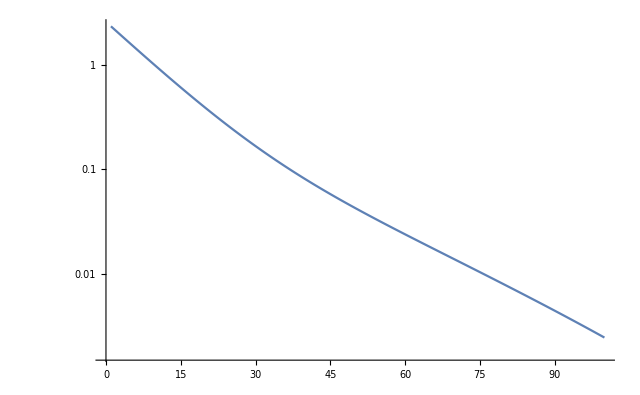

```mathematica
ListLogPlot[dRdE,Joined->True]
```

## Monte-Carlo Simulations

#### SI

```mathematica
dataMC=Import["DS_sim_SI.dat"];
```

```mathematica
dataMC[[1;;7]]
```

{{-e,//Asimov,Simulation},{//WIMP,pars:,Mx,=,100.},{//Detectors:},{//,XENON:,exp.,=,10.,kg*days,,Atomic,mass,=,131.29,,191,events},{//,CDMS_Ge:,exp.,=,1.,kg*days,,Atomic,mass,=,73.00,,254,events},{P,-2Log(L),Mx,C1,rho,v0,vesc,vEp,vSp,C15,C14,C13,C12},{1.0080796943043239×10^-99,484.78243795740258,1529.8426132924258,0.00011125400138890114,0.35831203776169901,0.00085820440477026017,0.0017622679839022681,0.,0.000017333333333333332,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

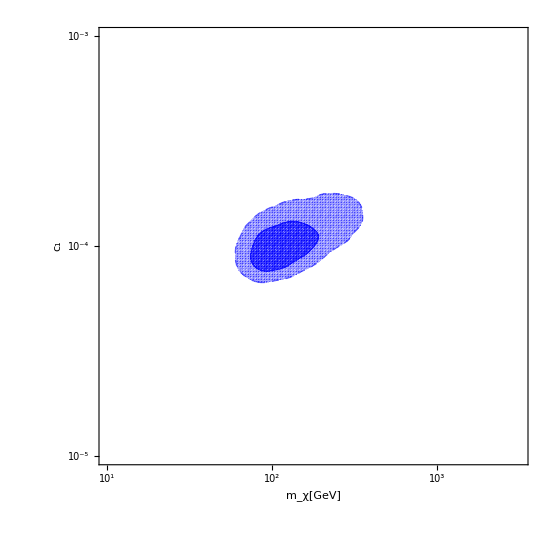

```mathematica
LogLogCrediblePlot[dataMC[[8;;All,{3,4,1}]],40,PlotRange->{{1,3.5},{-5,-3}},FrameLabel->{"m_χ[GeV]","c_1"}]
```

#### SD

```mathematica
dataMC=Import["DS_sim_SI.dat"];
```

```mathematica
dataMC[[1;;7]]
```

{{-e,//Asimov,Simulation},{//WIMP,pars:,Mx,=,100.},{//Detectors:},{//,XENON:,exp.,=,10.,kg*days,,Atomic,mass,=,131.29,,191,events},{//,CDMS_Ge:,exp.,=,1.,kg*days,,Atomic,mass,=,73.00,,254,events},{P,-2Log(L),Mx,C1,rho,v0,vesc,vEp,vSp,C15,C14,C13,C12},{1.0080796943043239×10^-99,484.78243795740258,1529.8426132924258,0.00011125400138890114,0.35831203776169901,0.00085820440477026017,0.0017622679839022681,0.,0.000017333333333333332,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
LogLogCrediblePlot[dataMC[[8;;All,{3,4,1}]],40,PlotRange->{{1,3.5},{-5,-3}},FrameLabel->{"m_χ[GeV]","c_1"}]
```

-Graphics-

#### SD+SI

```mathematica
dataMC=Import["DS_sim.dat"];
```

```mathematica
dataMC[[1;;5]]//MatrixForm
```

({//,Asimov,simulation}
{//,WIMP,pars:,spin-0.5,,Mx,=,100,,C1,=,0.0001,,C2,=,0}
{//,Detectors,used:}
{XENON,-,10,t.y,,nEvents,=,192.833}
{//,P,-2Log(L),Mx,C1,rho,v0,vesc})

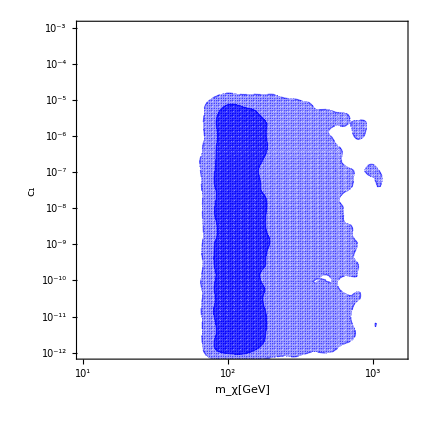

```mathematica
LogLogCrediblePlot[dataMC[[8;;All,{3,4,1}]],40,PlotRange->{{1,3.2},{-12,-3}},FrameLabel->{"m_χ[GeV]","c_1"}]
```

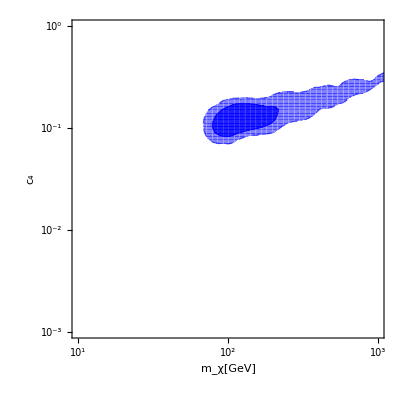

```mathematica
LogLogCrediblePlot[dataMC[[8;;All,{3,5,1}]],80,PlotRange->{{1,3},{-3,0}},FrameLabel->{"m_χ[GeV]","c_4"}]
```

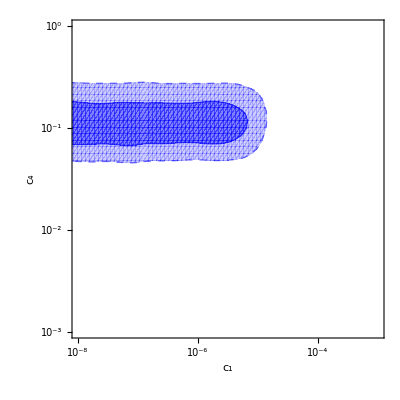

```mathematica
LogLogCrediblePlot[dataMC[[8;;All,{4,5,1}]],40,PlotRange->{{-8,-3},{-3,0}},FrameLabel->{"c_1","c_4"}]
```

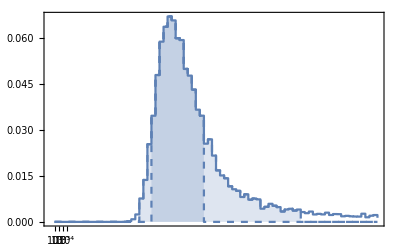

```mathematica
LogCrediblePlot1D[dataMC[[7;;All,{3,1}]],80]
```

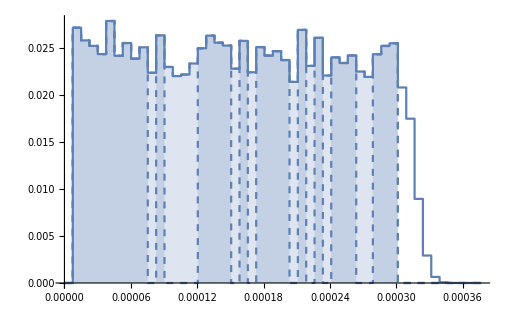

```mathematica
LogCrediblePlot1D[dataMC[[7;;All,{4,1}]],50]
```

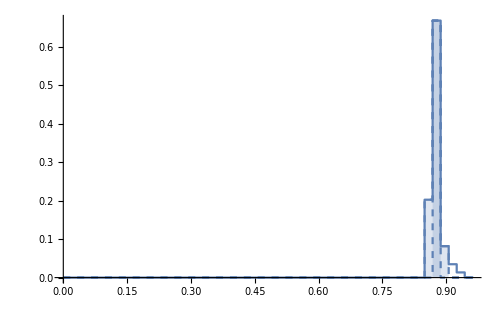

```mathematica
LogCrediblePlot1D[dataMC[[7;;All,{5,1}]],50]
```

#### Test

```mathematica
data=Import["DS_sim_test.dat"]
```

{{//,Asimov,simulation},{//,WIMP,pars:,spin-0.5,,Mx,=,100,,C1,=,0.0001,,C2,=,0},13273,{0.00012990579028494058,10.648667707985425,83.626393907546813,0.000075189436482410289,0.46652245718914548,0.00080826213167404875,0.0016550548415432283,0.,0.000017333333333333332,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

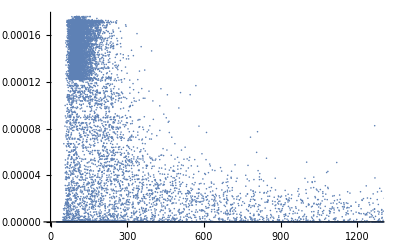

```mathematica
ListPlot[data[[7;;All,{3,1}]]]
```

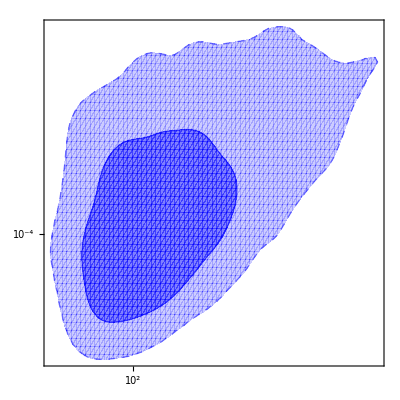

```mathematica
LogLogCrediblePlot2D[data[[7;;All,{3,4,1}]],50]
```

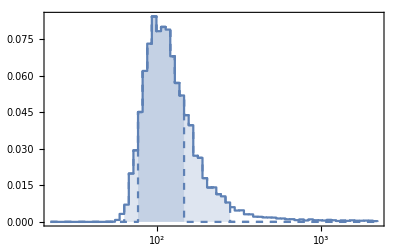

```mathematica
LogCrediblePlot1D[data[[7;;All,{3,1}]],70]
```